# SamplePublisher/AdvancedSamplePaclet

A complete sample Paclet that includes library resources

## Paclet

### Paclet Directory

NotebookDirectory[]

### Manifest

"Documentation"

"English"

"ReferencePages"

"Symbols"

"AddOne.nb"Documentation/English/ReferencePages/Symbols/AddOne.nb

"AddTwo.nb"Documentation/English/ReferencePages/Symbols/AddTwo.nb

"Kernel"

"AdvancedSamplePaclet.wl"Kernel/AdvancedSamplePaclet.wl

"LibraryResources"

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

"Scripts"

"Compile.wls"Scripts/Compile.wls

"SetBuildDate.wls"Scripts/SetBuildDate.wls

"Source"

"AddOne.c"Source/AddOne.c

"AddTwo.c"Source/AddTwo.c

"Library.c"Source/Library.c

"Tests"

"AddOne.wlt"Tests/AddOne.wlt

"AddTwo.wlt"Tests/AddTwo.wlt

## Web Content

### Headline Image

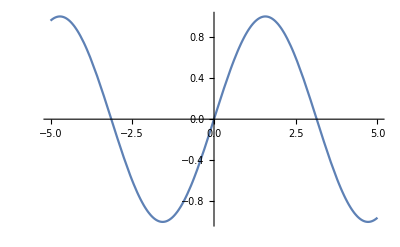

```mathematica
Plot[Sin[x],{x,-5,5}]
```

### Basic Description

A paragraph that describes your paclet in more detail.

### Details

Additional information about the paclet.

### Main Guide Page

File["path/to/guide.nb"]

## Examples

### Initialization for Examples

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Scripts","Compile.wls"}]];
```

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["SamplePublisher`AdvancedSamplePaclet`"];
```

### Basic Examples

Here is a basic example:

```mathematica
AddOne[1]
```

2

Here's another example:

```mathematica
AddOne[1]
```

2

```mathematica
AddTwo[1]
```

3

### Scope

## Source & Additional Information

### Creator

Sample Author

### Source Control Repository

https://github.com/WolframResearch/PacletCICD-Examples-AdvancedSample

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

sample

paclet

CI/CD

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

GitHub - WolframResearch/PacletCICD: Continuous integration and deployment for Wolfram Language Paclets

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

### Disclosures

DisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more informationLocal files

DisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more informationWolfram account

DisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more informationExternal services

DisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates, modifies or deletes symbols outside of the Publisher`PacletBaseName` context
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more informationWL system configuration

DisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more informationOS configuration

DisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more informationLocal system interactions

DisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more informationOther

## Author Notes

Additional information about limitations, issues, etc.